```mathematica
f[{x_,y_}]=x^2+y^2;
ϕ[r_]:=ⅇ^(-(.5r)^2)//N;
data=RandomReal[{0,π},{30,2}];
size=Dimensions[data]⟦1⟧;
ϕM=Table[ϕ[Norm[data⟦i⟧-data⟦j⟧]],{i,1,size},{j,1,size}]//N;
fv=Table[f[data⟦i⟧],{i,1,size}]//N;
w=LinearSolve[ϕM,fv]//N;
s[{x_,y_}]=∑_(k=1)^size w⟦k⟧ϕ[Norm[{x,y}-data⟦k⟧]];
Plot3D[{s[{x,y}],f[{x,y}]},{x,0,π},{y,0,π},PlotRange->All]
```

-Graphics3D-

```mathematica
plots=Table[w⟦k⟧ϕ[Norm[{x,y}-data⟦k⟧]],{k,1,size}];
Plot3D[plots,{x,0,π},{y,0,π},PlotRange->All]
```

-Graphics3D-

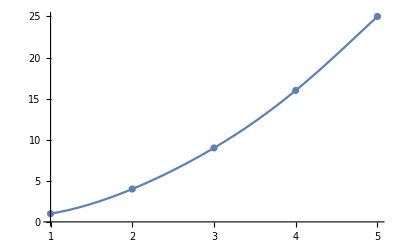

```mathematica
data = ({{1, 2, 3, 4, 5}, {1, 4, 9, 16, 25}});
ϕ[x1_,x2_,m_] = ⅇ^(-m ((√((x1-x2)^2))^2));
A = Table[ϕ[data⟦1,i⟧,data⟦1,j⟧,.1],{i,1,5},{j,1,5}];
f = data⟦2,All⟧;
λ=LinearSolve[A,f];
s[x_]=∑_(i=1)^5 λ⟦i⟧ϕ[x,data⟦1,i⟧,.1];
Show[Plot[s[x],{x,1,5}],
ListPlot[dataᵀ]]
```

```mathematica
λ
```

{93.6018,-338.301,553.567,-498.672,223.795}

```mathematica
ϕ[x1_,x2_,m_] = (√((x1-x2)^2))^m
ϕx[x_,xi_,m_]=D[ϕ[x,xi,m], x]
ϕx2[x_,xi_,m_]=m*Abs[x1-x2]^(m-1)
```

((x1-x2)^2)^(m/2)

m (x-xi) ((x-xi)^2)^(-1+m/2)

```mathematica
Simplify[m (x-xi) ((x-xi)^2)^(-1+m/2)]
```

(m ((x-xi)^2)^(m/2))/(x-xi)

```mathematica
ϕx[0,2,3]
```

-12